# MTH 1220 Math & Art

## Getting Mathematica The school has a site license allowing all students to download the software onto their laptops. There is a link to a How-to page in blackboard https://service.northeastern.edu/tech?id=kb_article&sys_id=4e04d728dbfd3740a37cd206ca96198e Additionally Mathematica is on all computers in labs through campus

## Activating a Mathematica Command

<shift><enter>

    After typing in your Mathematica command or program
    you need to hold down the <shift>-key and press <enter or return>-key
    
NOTE:  The actual Program Code is IN THE YELLOW CELLS
       Click anywhere in the YELLOW-CELL 
       and then Press <shift><enter>

## File Location - Saving Images

### Saving your Mathematica File

Save your Mathematica program in some location you will remember.

### The following Sets The Directory. Any image you "Export" will be in the same location as this Notebook

```mathematica
SetDirectory[ NotebookDirectory[] ]
```

#### A Quick Example - (run the following - then check that the sphere.jpg has been saved.)

```mathematica
sphere =Graphics3D[     
					{Sphere[]},
					{Boxed-> False}
				]

Export[ "sphere.jpg", sphere ]
```

sphere.jpg

A Minimal HTML File to display the image.
Create a file called "sphere.html"
containing the following code.

<HTML>
<H2>Here is the sphere image made in Mathematica</H2>
<IMG SRC="sphere.jpg">
</HTML>

## Getting Help: ? .... *

### ?Grap* <-- will bring up information on all commands beginning with "Grap" You can always use the Web to search for help.

```mathematica
?Graphic*
```

## Graphics Primitives -- Use these to make your drawing.

The COMMAs are the LIST-Seperater

### Format: This is the Format

Graphics[
 		  { 
  			a list of Graphics Primitives
  		  },
 
 		  {
  			a list of Settings (options)
  	      }
        ]

### Primitives:

Point[ {x,y} ]
	
	Line[ {  {x1,y1},{x2,y2}, ..., {xn,yn}  }]
	
	Polygon[{ 
				{x1,y1},{x2,y2}, ..., {xn,yn}  
		   }]
		   
	Circle[ {Xcenter,Ycenter}, radius ]
	Circle[ {Xcenter,Ycenter}, {radius1, radius2} ]
	Circle[ {Xcenter,Ycenter}, {radius1, radius2}, {angle1,angle2} ]
	
	Disk[...same as Circle...]
	
	Text[ "some text", {x,y} ]

#### A Quick Example

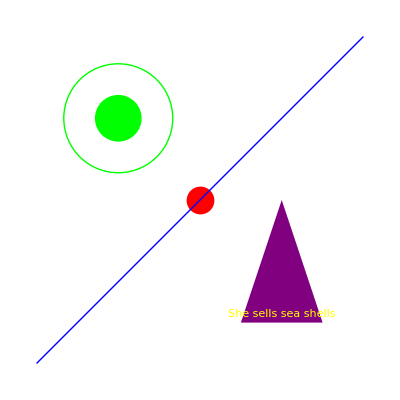

```mathematica
Graphics[

		{
			Red, PointSize[ 0.05 ], Point[{0,0}],

			Blue, Thick, Line[{ {-1,-1}, {1,1} } ] ,

			Green, Circle[ {-1/2, 1/2}, 1/3 ],
		
				       Disk[  {-1/2, 1/2}, 1/7 ],

			Purple, Polygon[{
							{0.25, -0.75}, 
							{0.75, -0.75},
							{0.50,   0 }
						} ],

			Yellow, Text["She sells sea shells", {1/2, -0.70} ]
	       }

		]
```

### Settings:

PlotRange -> { {Xmin,Xmax}, {Ymin,Ymax} }

	AspectRatio -> #
	
	GridLines -> { {x1, x2, ..., xn}, {y1, y2, ..., ym} }
	GridLinesStyle -> Directive[ Gray, Thin, Dashed ]
	
	Axes -> True/False

### A Useful Example of Settings (Use this while creating your Motief. Then for the final piece, get rid of the SETTINGS)

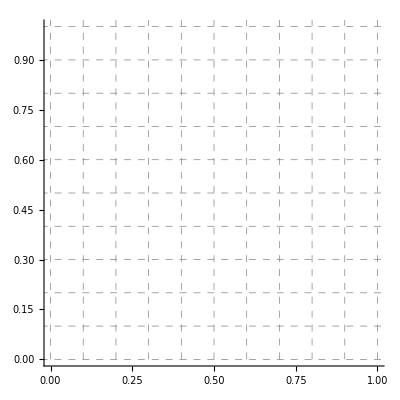

```mathematica
SETTINGS = {
			PlotRange-> { {0,1},{0,1} },
			GridLines -> { {0, .1, .2, .3, .4, .5, .6, .7, .8, .9, 1.0},
						{0, .1, .2, .3, .4, .5, .6, .7, .8, .9, 1.0} },
			GridLinesStyle -> Directive[ Gray, Thin, Dashed],
			Axes-> True
		};
Graphics[{ }, {SETTINGS} ]
```

#### A Quick Example

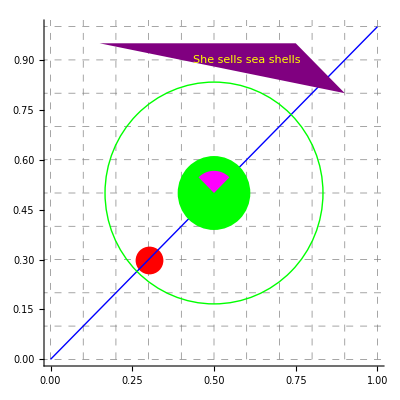

```mathematica
Graphics[

mymotief ={
			Red, PointSize[ 0.05 ], Point[{.3,.3}],

			Blue, Thick, Line[{ {0,0}, {1,1} } ] ,

			Green, Circle[ {1/2, 1/2}, 1/3 ],
				       Disk[  {1/2, 1/2}, 1/9 ],

			Magenta,  Disk[  {1/2, 1/2}, 1/15, {45 Degree, 135 Degree} ],

			Purple, Polygon[{
							{0.15, 0.95}, 
							{0.75, 0.95},
							{0.9,   .8 }
						} ],

			Yellow, Text["She sells sea shells", {.6, 0.90} ]
	       },

		{SETTINGS}
		]
```